Placed::labpos: Placed[{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Wordle,Waterworks!,Warfare Area 3,Twisted Rope 3D,Tunnel Rush,Tug of War with Cars,Truck Space 2,Touhou: Luminous Strike,Tomodatchi Collection,Time Shooter 3,The Typing Game,There is no game,🤑💰💸The Fruits🤑💰💸,The Bauble Factory,Tetris,Terraria},#1&] is not a valid position for the placement of labels.

Placed::labpos: #1& is not a valid position for the placement of labels.

General::stop: Further output of Placed::labpos will be suppressed during this calculation.

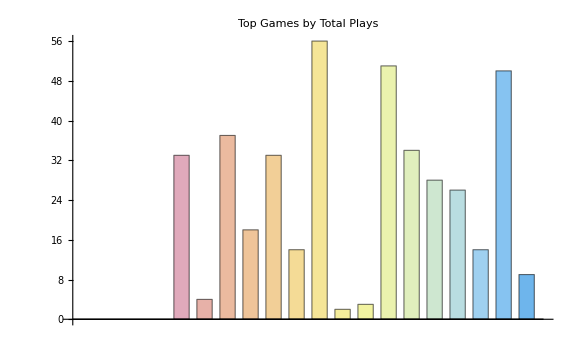

```mathematica
(*Published CSV link*)sheetURL="https://docs.google.com/spreadsheets/d/e/2PACX-1vTf-6AlCge2OKAs4JuAPi5cPtJWmGqjMy27zGyTheWlWiToV4MxwCel0E_YiMiK11QpF69v-EW8bi78/pub?output=csv";

(*Import data*)
data=Import[sheetURL,"CSV"];

(*Separate headers and values*)
headers=First[data];
values=Rest[data];

(*Convert total plays to numbers,replace missing/non-numeric with 0*)
cleanValues=values/. {title_,count_}:>{title,If[StringQ[count]&&StringMatchQ[count,NumberString],ToExpression[count],0]};

(*Optional:sort descending by total plays*)
cleanValues=Reverse@SortBy[cleanValues,Last];

(*Show top N games for readability*)
topN=20;

BarChart[cleanValues[[;;Min[topN,Length[cleanValues]],2]],ChartLabels->Placed[cleanValues[[;;Min[topN,Length[cleanValues]],1]],Rotate[#,45 Degree]&],PlotLabel->"Top Games by Total Plays",ImageSize->Large,ChartStyle->"Pastel",BarSpacing->0.5]
```